# Calculate entanglement monotone

Determine if [sub]systems are entangled and quantify it

## Example Content

In Wolfram quantum framework, one can test if part of a quantum system is entangled with another part, and also quantify the amount of entanglement, using different measures.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

Show formula of W-state for 4-qubits:

```mathematica
ψ=QuantumState[{"W",4}];
ψ["Formula"]
```

1/2 0001+1/2 0010+1/2 0100+1/2 1000

One can calculate different quantum entanglement monotone using the function QuantumEntanglementMonotone. Many different monotones are supported, such as concurrence, negativity, log-negativity, entanglement entropy, Renyi entropy, and realignment.

Calculate the Concurrence:

```mathematica
QuantumEntanglementMonotone[ψ,"Concurrence"]
```

(√3)/2

Given a Werner state of 1-qubits, with the probability p, calculate the Negativity:

```mathematica
$Assumptions=p∈Reals;
FullSimplify@QuantumEntanglementMonotone[QuantumState[{"Werner",p,2}],"Negativity"]
```

1/4 (-2+Abs[1-2 p]+Abs[3-2 p])

Create a random graph:

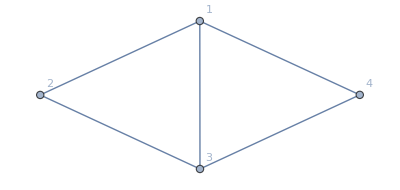

```mathematica
g=RandomGraph[{4,5},VertexLabels->"Name"]
```

Create corresponding graph-state:

```mathematica
ϕ=QuantumState[{"Graph",g}];
```

One can also test if two systems are entangled or not, using the function QuantumEntangledQ.

Show that qubits that are connected by an edge, are entangled:

```mathematica
QuantumEntangledQ[ϕ,List@@#]&/@EdgeList[g]
```

{True,True,True,True,True}

Plot different types of entanglement monotone for state β00+√(1-β^2)11:

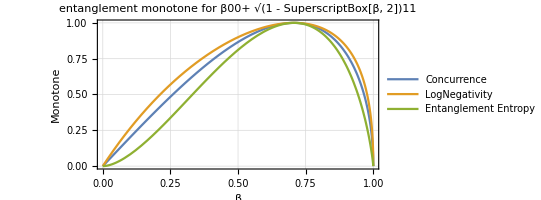

```mathematica
Plot[{QuantumEntanglementMonotone[QuantumState[{β,0,0,Sqrt[1-β^2]}],{{1},{2}},"Concurrence"],
	QuantumEntanglementMonotone[QuantumState[{β,0,0,Sqrt[1-β^2]}],{{1},{2}},"LogNegativity"],
	QuantumEntanglementMonotone[QuantumState[{β,0,0,Sqrt[1-β^2]}],{{1},{2}},"EntanglementEntropy"]},{β,0,1}, PlotLegends->{"Concurrence", "LogNegativity", "Entanglement Entropy"},Frame->True,PlotLabel->"entanglement monotone for β00+ √(1 - SuperscriptBox[β, 2])11",FrameLabel->{"β","Monotone"},GridLines->Automatic,AspectRatio->1/2]
```

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

-Graphics-

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Quantum Entanglement

Entanglement Monotone

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/ref/QuantumEntangledQ.html

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/ref/QuantumEntanglementMonotone.html

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.